## Preamble and prep

```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->16,FontColor->Black};
```

```mathematica
exportImages=True;
ExportToIMGFolder[cmd_,filename_]:=Module[{},If[exportImages,Export[StringJoin[ParentDirectory@NotebookDirectory[],"/tex/pictures/"]<>filename<>".svg",cmd/.{EdgeForm[],r_?ColorQ,i___}:>{EdgeForm[r],r,i},"SVG"],Null];
cmd]
```

```mathematica
IntegrateWithNoAccel[mass_,est_,Lst_]:=IntegrateWithNoAccel[mass,est,Lst]=
NIntegrate[-1/(√(est^2-(1+(Lst^2 mass^2)/y^2)(1-(2mass)/y))),{y,2mass,0}]
```

## Functions for R (numerical, Carlson) and L

```mathematica
ropt[M_,a_,e0_]:=If[a==0,-1,2M+e0/a]
NτR[M_,a_,e0_,r_]:=NIntegrate[1/(z √(2 M z^3+( -(-2 a e0 - 4 a^2 M)*M+2a e0 M-1+e0^2) z^2+(-2 a e0 - 4 a^2 M) z+a^2)),{z,1/r,∞}]
Nτ[M_,a_,e0_]:=NτR[M,a,e0,2M]
NτOptimal[M_,a_,e0_]:=NτOptimal[M,a,e0]=Module[{rbang},
rbang=ropt[M,a,e0];
If[2M>=rbang>=0,
Nτ[M,a,e0]-NτR[M,a,e0,rbang]+NτR[M,0,0,rbang],
Nτ[M,a,e0]
]
]
rLopt[M_,a_,L0_]:=If[a==0,z==-1,Reduce[L0-a(-1/2 √(-1+(2 M)/z) z (3 M+z)-3 M^2 ArcTan[√(-1+(2 M)/z)])==0,{z},Reals]]
NτLR[M_,a_,L0_,r_]:=NIntegrate[-(1/(√(-(1+1/z^2(L0-a(-1/2 √(-1+(2 M)/z) z (3 M+z)-3 M^2 ArcTan[√(-1+(2 M)/z)]))^2)(1-(2M)/z)))),{z,r,0}]
NτL[M_,a_,L0_]:=NτLR[M,a,L0,2M]
NτLOptimal[M_,a_,L0_]:=(*NτLOptimal[M,a,L0]=*)Module[{rbang},
rbang=rLopt[M,a,L0];
If[Not[BooleanQ[rbang]] && 2M>=rbang[[2]]>=0,
NτL[M,a,L0]-NτLR[M,a,L0,rbang[[2]]]+NτLR[M,0,0,rbang[[2]]],
NτL[M,a,L0]
]
]
```

Carlson integrals give the best results due to avoiding unnecessary branch cuts:

```mathematica
CarlsonFromR[M_,a_,e0_,r_]:=CarlsonFromR[M,a,e0,r]=Module[{z1,z2,z3,ρ},
{z1,z2,z3}=-Flatten@Values@List@ToRules@Roots[( z^3+( -(- a e0 - 2 a^2 M))z^2+(a e0 -1/(2M)+e0^2/(2M)) z^2+(-a e0/M - 2 a^2 ) z+1/(2M)a^2)==0,z]+1/r;
ρ=1/r;
2/3 CarlsonRJ[z1,z2,z3,ρ]/Sqrt[2M]]
Carlson[M_,a_,e0_]:=CarlsonFromR[M,a,e0,2M]
CarlsonOptimal[M_,a_,e0_]:=(*CarlsonOptimal[M,a,e0]=*)Module[{rbang},
If[a==0,
Carlson[M,0,e0],
rbang=ropt[M,a,e0];
If[2M>=rbang>0,
Carlson[M,a,e0]-CarlsonFromR[M,a,e0,rbang]+CarlsonFromR[M,0,0,rbang],
Carlson[M,a,e0]
]
]
]
```

```mathematica
(CarlsonOptimal[1500*5*10^10,-100/9000000000000000,1]//N//Re)/(CarlsonOptimal[1500*5*10^10,0,1]//N)
```

1.27932

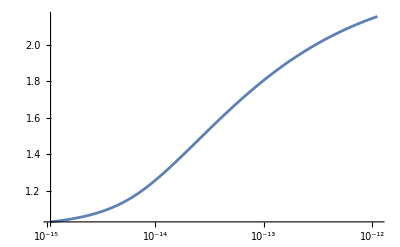

```mathematica
LogLinearPlot[(CarlsonOptimal[1500*5*10^10,-a,1]//N//Re)/(CarlsonOptimal[1500*5*10^10,0,1]//N),{a,0,10000/9000000000000000},PlotRange->All]
```

We can use Legendre integrals too:

```mathematica
CarlsonToEll[M_,a_,e0_]:=CarlsonToEll[M,a,e0]=Module[{x,y,z,rho,ϕ,k,αsq},
{z,y,x}=-Flatten@Values@List@ToRules@Roots[( z^3+( -(- a e0 - 2 a^2 M))z^2+(a e0 -1/(2M)+e0^2/(2M)) z^2+(-a e0/M - 2 a^2 ) z+1/(2M)a^2)==0,z]+1/(2M);
rho=1/(2M);
αsq=(z-rho)/(z-x);
k=√((z-y)/(z-x));
ϕ=ArcCos[√(x/z)];
Print[{αsq,k,ϕ}];
2/3 1/Sqrt[2M](3/αsq(EllipticPi[αsq,ϕ,k^2]-EllipticF[ϕ,k^2]))/(z-x)^(3/2)
]
```

```mathematica
CarlsonToEll[1,-0.65,1]//Chop
```

{0.476013-0.152594 ⅈ,0.952268-0.305265 ⅈ,1.19838+0.423973 ⅈ}

1.63458

## data for r graphs

```mathematica
dataCarlsonOptimal=Flatten[Table[{a,e0,CarlsonOptimal[1,a,e0]//N//Re},{a,-5,0,0.05},{e0,0,5,0.05}],1];
```

```mathematica
dataCarlsonGain=({#[[1]],#[[2]],#[[3]]/IntegrateWithNoAccel[1,#[[2]],0]})&/@dataCarlsonOptimal
```

-Graphics3D-

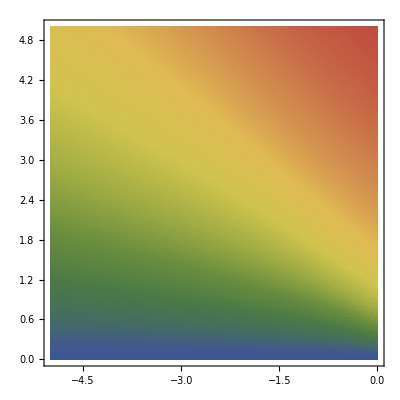

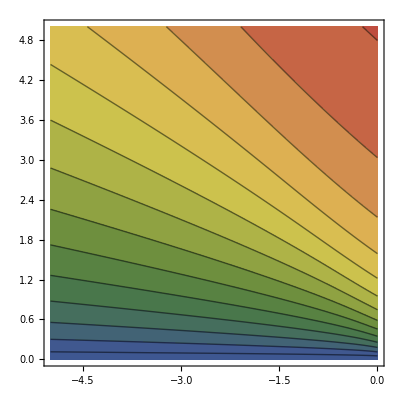

```mathematica
(*ListPlot3D[dataCarlsonOptimal,ColorFunction->Function[{x,y,par},ColorData["DarkRainbow"][1-par/π]],ColorFunctionScaling->False,MeshFunctions->{#3&},Mesh->{Range[0,π,π/16]}]*)
ExportToIMGFolder[ListPlot3D[dataCarlsonOptimal,ColorFunction->Function[{x,y,par},ColorData["DarkRainbow"][1-par/π]],ColorFunctionScaling->False,LabelStyle->texStyle,AxesLabel->MaTeX/@{"\\alpha [m^{-1}]","e_0","\\tau [m]"},BaseStyle->texStyle,AxesStyle->Black,BoxStyle->Black],"e-a-tau-3dplot"
]
ListDensityPlot[dataCarlsonOptimal,ColorFunction->(ColorData["DarkRainbow"][1-#/π]&),ColorFunctionScaling->False]
ExportToIMGFolder[ListContourPlot[dataCarlsonOptimal,ColorFunction->(ColorData["DarkRainbow"][1-#/π]&),ColorFunctionScaling->False,Contours->Range[π,0,-π/16],PlotLegends->BarLegend[Automatic,LegendLabel->MaTeX@"\\tau [m]"],LabelStyle->texStyle,FrameLabel->MaTeX/@{"\\alpha [m^{-1}]","e_0"},PlotRange->All,FrameStyle->Black],"e-a-tau-contourplot"]
```

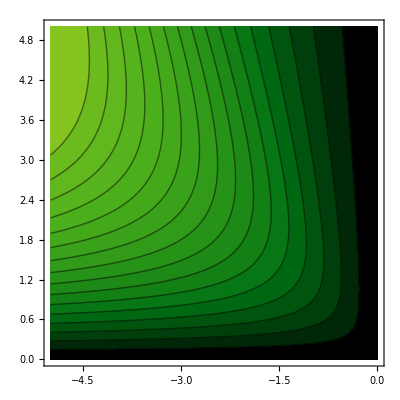

```mathematica
(*ExportToIMGFolder[ListPlot3D[dataCarlsonGain,BaseStyle->texStyle,ColorFunction->Function[{x,y,par},ColorData["AvocadoColors"][Log[5,par]]],ColorFunctionScaling->False,AxesStyle->Black,BoxStyle->Black,AxesLabel->MaTeX/@{"\\alpha [m^{-1}]","e_0","\\tau [m]"}],"e-a-tau-gainplot"]*)
ExportToIMGFolder[ListContourPlot[dataCarlsonGain,Contours->16,ColorFunction->(ColorData["AvocadoColors"][Log[5,#]]&),ColorFunctionScaling->False,PlotLegends->BarLegend[Automatic,LegendLabel->MaTeX@"\\frac{\\tau}{\\tau_{\\alpha=0}}"],BaseStyle->texStyle,LabelStyle->texStyle,FrameLabel->MaTeX/@{"\\alpha [m^{-1}]","e_0"},PlotRange->All,FrameStyle->Black],"e-a-tau-gaincontourplot"]
```

## Data for L graphs

```mathematica
dataNLOptimal=Flatten[Table[{a,L0,NτLOptimal[1,a,L0]//N//Re},{a,-5,0,0.5/10},{L0,0,5,0.5/10}],1];
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

```mathematica
dataNLGain=({#[[1]],#[[2]],#[[3]]/IntegrateWithNoAccel[1,0,#[[2]]]})&/@dataNLOptimal
```

-Graphics3D-

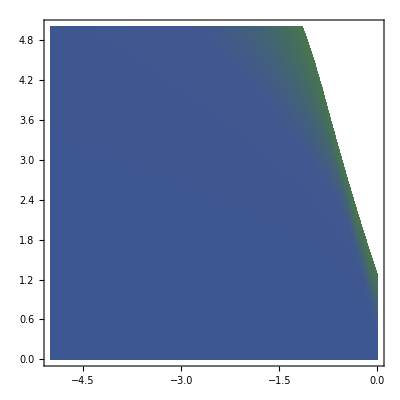

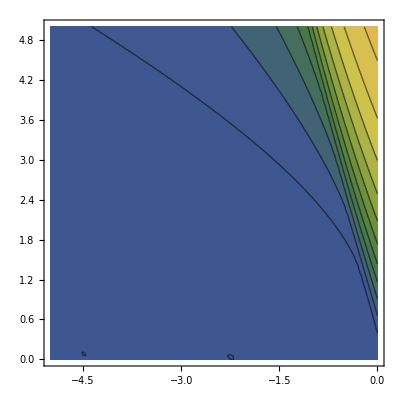

```mathematica
ExportToIMGFolder[ListPlot3D[dataNLOptimal,ColorFunction->Function[{x,y,par},ColorData["DarkRainbow"][1-par/π]],ColorFunctionScaling->False,AxesLabel->MaTeX/@{"\\alpha [m^{-1}]","L_0 [M]","\\tau [m]"},BaseStyle->texStyle,LabelStyle->texStyle,AxesStyle->Black,BoxStyle->Black,PlotRange->All],"l-a-tau-3dplot"]
ListDensityPlot[dataNLOptimal,ColorFunction->(ColorData["DarkRainbow"][1-#/π]&),ColorFunctionScaling->False]
ExportToIMGFolder[ListContourPlot[dataNLOptimal,ColorFunction->(ColorData["DarkRainbow"][1-#/π]&),ColorFunctionScaling->False,Contours->Range[π,0,-π/16],PlotLegends->BarLegend[Automatic,LegendLabel->MaTeX@"\\tau [m]"],LabelStyle->texStyle,BaseStyle->texStyle,FrameLabel->MaTeX/@{"\\alpha [m^{-1}]","L_0 [M]"},PlotRange->All,FrameStyle->Black],"l-a-tau-contourplot"]
```

-Graphics3D-

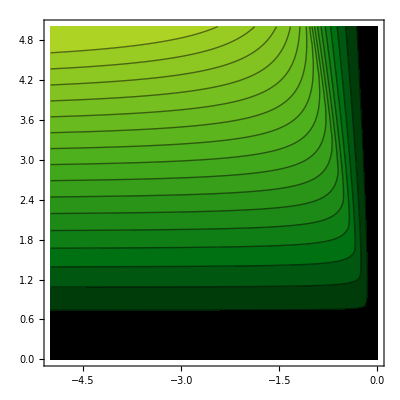

```mathematica
ExportToIMGFolder[ListPlot3D[dataNLGain,ColorFunction->Function[{x,y,par},ColorData["AvocadoColors"][Log[5,par]]],ColorFunctionScaling->False,AxesLabel->MaTeX/@{"\\alpha [m^{-1}]","L_0 [M]","\\tau [m]"},BaseStyle->texStyle,LabelStyle->texStyle,AxesStyle->Black,BoxStyle->Black],"l-a-tau-gainplot"]
ExportToIMGFolder[ListContourPlot[dataNLGain,Contours->16,ColorFunction->(ColorData["AvocadoColors"][Log[5,#]]&),ColorFunctionScaling->False,PlotLegends->BarLegend[Automatic,LegendLabel->MaTeX@"\\frac{\\tau}{\\tau_{\\alpha=0}}"],BaseStyle->texStyle,LabelStyle->texStyle,FrameLabel->MaTeX/@{"\\alpha [m^{-1}]","L_0 [M]"},PlotRange->All,FrameStyle->Black],"l-a-tau-gaincontourplot"]
```

## Generation of data for LATEX table of results

```mathematica
ColumnForm[Table[{e0,CarlsonOptimal[1,0,e0],CarlsonOptimal[1,0,e0]//N},{e0,{-1,-0.1,0,0.01,0.1,1,10}}]]
```

{-1,4/3,1.33333}
{-0.1,2.78391,2.78391}
{0,π,3.14159}
{0.01,3.10206,3.10206}
{0.1,2.78391,2.78391}
{1,4/3,1.33333}
{10,1/99 √2 (10 √2-CarlsonRC[50,1/2]),0.195943}

```mathematica
ColumnForm[Table[{a,Carlson[1,a,1],Carlson[1,a,1]//N//Chop},{a,{0,-0.65,-2.4, -10}}]]
```

{0,4/3,1.33333}
{-0.65,1.63458-1.81563×10^-19 ⅈ,1.63458}
{-2.4,1.63631+6.81836×10^-17 ⅈ,1.63631}
{-10,1/3 √2 CarlsonRJ[121/2+(314 35^(2/3))/(3 (57015-√105))^(1/3)+(35 (57015-√105))^(1/3)/3^(2/3),121/2-(157 35^(2/3) (1+ⅈ √3))/(3 (57015-√105))^(1/3)-((1-ⅈ √3) (35 (57015-√105))^(1/3))/(2 3^(2/3)),121/2-(157 35^(2/3) (1-ⅈ √3))/(3 (57015-√105))^(1/3)-((1+ⅈ √3) (35 (57015-√105))^(1/3))/(2 3^(2/3)),1/2],0.726011}

```mathematica
ColumnForm[Table[{a,Carlson[2,a,1],Carlson[2,a,1]/2//N//Chop},{a,{0,-0.65,-2.4, -10}}]]
```

{0,8/3,1.33333}
{-0.65,3.58005+3.41505×10^-19 ⅈ,1.79002}
{-2.4,2.34927+1.27566×10^-16 ⅈ,1.17463}
{-10,1/3 CarlsonRJ[1523/12-(28997 5^(2/3) (1+ⅈ √3))/(3 2^(2/3) (22082315-3 √11085)^(1/3))-1/6 (1-ⅈ √3) (5/2 (22082315-3 √11085))^(1/3),1523/12-(28997 5^(2/3) (1-ⅈ √3))/(3 2^(2/3) (22082315-3 √11085)^(1/3))-1/6 (1+ⅈ √3) (5/2 (22082315-3 √11085))^(1/3),1/4+1/3 (380+28997 5^(2/3) (2/(22082315-3 √11085))^(1/3)+(5/2 (22082315-3 √11085))^(1/3)),1/4],0.435446}

```mathematica
ColumnForm[Table[{a,CarlsonOptimal[1,a,1],CarlsonOptimal[1,a,1]//N//Chop},{a,{0,-0.65,-2.4, -10}}]]
```

{0,4/3,1.33333}
{-0.65,1.63472-1.81563×10^-19 ⅈ,1.63472}
{-2.4,2.0537+6.68805×10^-17 ⅈ,2.0537}
{-10,-√2 ((√(19/2))/10-CarlsonRC[1/38,10/19])+1/3 √2 CarlsonRJ[121/2+(314 35^(2/3))/(3 (57015-√105))^(1/3)+(35 (57015-√105))^(1/3)/3^(2/3),121/2-(157 35^(2/3) (1+ⅈ √3))/(3 (57015-√105))^(1/3)-((1-ⅈ √3) (35 (57015-√105))^(1/3))/(2 3^(2/3)),121/2-(157 35^(2/3) (1-ⅈ √3))/(3 (57015-√105))^(1/3)-((1+ⅈ √3) (35 (57015-√105))^(1/3))/(2 3^(2/3)),1/2]-1/3 √2 CarlsonRJ[1150/19+(314 35^(2/3))/(3 (57015-√105))^(1/3)+(35 (57015-√105))^(1/3)/3^(2/3),1150/19-(157 35^(2/3) (1+ⅈ √3))/(3 (57015-√105))^(1/3)-((1-ⅈ √3) (35 (57015-√105))^(1/3))/(2 3^(2/3)),1150/19-(157 35^(2/3) (1-ⅈ √3))/(3 (57015-√105))^(1/3)-((1+ⅈ √3) (35 (57015-√105))^(1/3))/(2 3^(2/3)),10/19],2.48242}

```mathematica
ColumnForm[Table[{a,CarlsonOptimal[2,a,1],CarlsonOptimal[2,a,1]/2//N//Chop},{a,{0,-0.65,-2.4, -10}}]]
```

{0,8/3,1.33333}
{-0.65,3.69475+7.69793×10^-19 ⅈ,1.84738}
{-2.4,4.55337+1.57399×10^-16 ⅈ,2.27668}
{-10,-2 ((√39)/20-CarlsonRC[1/156,10/39])+1/3 CarlsonRJ[1523/12-(28997 5^(2/3) (1+ⅈ √3))/(3 2^(2/3) (22082315-3 √11085)^(1/3))-1/6 (1-ⅈ √3) (5/2 (22082315-3 √11085))^(1/3),1523/12-(28997 5^(2/3) (1-ⅈ √3))/(3 2^(2/3) (22082315-3 √11085)^(1/3))-1/6 (1+ⅈ √3) (5/2 (22082315-3 √11085))^(1/3),1/4+1/3 (380+28997 5^(2/3) (2/(22082315-3 √11085))^(1/3)+(5/2 (22082315-3 √11085))^(1/3)),1/4]-1/3 CarlsonRJ[1650/13-(28997 5^(2/3) (1+ⅈ √3))/(3 2^(2/3) (22082315-3 √11085)^(1/3))-1/6 (1-ⅈ √3) (5/2 (22082315-3 √11085))^(1/3),1650/13-(28997 5^(2/3) (1-ⅈ √3))/(3 2^(2/3) (22082315-3 √11085)^(1/3))-1/6 (1+ⅈ √3) (5/2 (22082315-3 √11085))^(1/3),10/39+1/3 (380+28997 5^(2/3) (2/(22082315-3 √11085))^(1/3)+(5/2 (22082315-3 √11085))^(1/3)),10/39],2.64195}

```mathematica
ColumnForm[Table[{a,NτL[1,a,3.5],NτLOptimal[1,a,3.5]//N//Chop},{a,{0,-0.65,-1.3,-2.4, -10}}]]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

{0,1.21238,1.21238}
{-0.65,2.16171,2.16171}
{-1.3,2.08303,2.80145}
{-2.4,1.45643,2.96286}
{-10,0.510874,3.09916}

Generating the table:

```mathematica
g=10/((3*10^8)^2)
```

1/9000000000000000

```mathematica
sol=1500
```

1500

```mathematica
ColumnForm[Flatten[Table[{M,a,e,CarlsonOptimal[M,a,e]//N//Re,CarlsonOptimal[M,a,e]/(3*10^8)//N//Re,CarlsonOptimal[M,a,e]/(3*10^8*60)//N//Re,CarlsonOptimal[M,a,e]/(3*10^8*60*60)//N//Re,CarlsonOptimal[M,a,e]/(3*10^8*60*60*24)//N//Re,(CarlsonOptimal[M,a,e]//N//Re)/(CarlsonOptimal[M,0,e]//N//Re)-1},{M,{4.297*10^6*sol,6.5*10^9*sol,4.07*10^10*sol,10^11 sol}},{a,{0,-g,-10g,-100g,-1000g}},{e,{1,10}}],1]]
```

{{6.4455×10^9,0,1,8.594×10^9,28.6467,0.477444,0.00795741,0.000331559,0.},{6.4455×10^9,0,10,1.26295×10^9,4.20983,0.0701639,0.0011694,0.0000487249,0.}}
{{6.4455×10^9,-1/9000000000000000,1,8.594×10^9,28.6467,0.477445,0.00795741,0.000331559,2.45543×10^-7},{6.4455×10^9,-1/9000000000000000,10,1.26055×10^9,4.20184,0.0700306,0.00116718,0.0000486324,-0.00189891}}
{{6.4455×10^9,-1/900000000000000,1,8.59402×10^9,28.6467,0.477446,0.00795743,0.000331559,2.45543×10^-6},{6.4455×10^9,-1/900000000000000,10,1.26294×10^9,4.20978,0.0701631,0.00116938,0.0000487243,-0.0000113972}}
{{6.4455×10^9,-1/90000000000000,1,8.59421×10^9,28.6474,0.477456,0.0079576,0.000331567,0.0000245546},{6.4455×10^9,-1/90000000000000,10,1.26296×10^9,4.20986,0.0701643,0.0011694,0.0000487252,5.76047×10^-6}}
{{6.4455×10^9,-1/9000000000000,1,8.59611×10^9,28.6537,0.477562,0.00795936,0.00033164,0.000245571},{6.4455×10^9,-1/9000000000000,10,1.26303×10^9,4.21011,0.0701685,0.00116948,0.0000487281,0.0000666028}}
{{9.75×10^12,0,1,1.3×10^13,43333.3,722.222,12.037,0.501543,0.},{9.75×10^12,0,10,1.91044×10^12,6368.14,106.136,1.76893,0.0737053,-1.11022×10^-16}}
{{9.75×10^12,-1/9000000000000000,1,1.30048×10^13,43349.4,722.491,12.0415,0.50173,0.000371494},{9.75×10^12,-1/9000000000000000,10,1.91064×10^12,6368.78,106.146,1.76911,0.0737128,0.000100768}}
{{9.75×10^12,-1/900000000000000,1,1.30484×10^13,43494.6,724.909,12.0818,0.503409,0.00372073},{9.75×10^12,-1/900000000000000,10,1.91237×10^12,6374.57,106.243,1.77071,0.0737797,0.00100875}}
{{9.75×10^12,-1/90000000000000,1,1.34905×10^13,44968.4,749.474,12.4912,0.520468,0.0377328},{9.75×10^12,-1/90000000000000,10,1.92994×10^12,6433.12,107.219,1.78698,0.0744574,0.0102042}}
{{9.75×10^12,-1/9000000000000,1,1.74299×10^13,58099.7,968.328,16.1388,0.67245,0.340762},{9.75×10^12,-1/9000000000000,10,2.13109×10^12,7103.64,118.394,1.97323,0.082218,0.115496}}
{{6.105×10^13,0,1,8.14×10^13,271333.,4522.22,75.3704,3.14043,0.},{6.105×10^13,0,10,1.19623×10^13,39874.4,664.573,11.0762,0.461509,-1.11022×10^-16}}
{{6.105×10^13,-1/9000000000000000,1,8.15895×10^13,271965.,4532.75,75.5459,3.14774,0.00232825},{6.105×10^13,-1/9000000000000000,10,1.19699×10^13,39899.5,664.992,11.0832,0.4618,0.000631336}}
{{6.105×10^13,-1/900000000000000,1,8.33127×10^13,277709.,4628.48,77.1414,3.21423,0.0234979},{6.105×10^13,-1/900000000000000,10,1.20384×10^13,40127.9,668.799,11.1466,0.464444,0.00635884}}
{{6.105×10^13,-1/90000000000000,1,1.0051×10^14,335035.,5583.91,93.0652,3.87772,0.234772},{6.105×10^13,-1/90000000000000,10,1.27823×10^13,42607.7,710.129,11.8355,0.493145,0.0685495}}
{{6.105×10^13,-1/9000000000000,1,1.45187×10^14,483957.,8065.95,134.433,5.60136,0.783626},{6.105×10^13,-1/9000000000000,10,3.60123×10^13,120041.,2000.68,33.3447,1.38936,2.01048}}
{{150000000000000,0,1,2.×10^14,666667.,11111.1,185.185,7.71605,0.},{150000000000000,0,10,2.93914×10^13,97971.4,1632.86,27.2143,1.13393,0.}}
{{150000000000000,-1/9000000000000000,1,2.01146×10^14,670486.,11174.8,186.246,7.76026,0.00572948},{150000000000000,-1/9000000000000000,10,2.94371×10^13,98123.6,1635.39,27.2565,1.13569,0.00155299}}
{{150000000000000,-1/900000000000000,1,2.1169×10^14,705633.,11760.6,196.009,8.16705,0.0584496},{150000000000000,-1/900000000000000,10,2.98561×10^13,99520.2,1658.67,27.6445,1.15185,0.0158082}}
{{150000000000000,-1/90000000000000,1,2.89604×10^14,965345.,16089.1,268.151,11.173,0.448018},{150000000000000,-1/90000000000000,10,3.50659×10^13,116886.,1948.1,32.4684,1.35285,0.193065}}
{{150000000000000,-1/9000000000000,1,3.90493×10^14,1.30164×10^6,21694.,361.567,15.0653,0.952463},{150000000000000,-1/9000000000000,10,1.91031×10^14,636771.,10612.9,176.881,7.37004,5.49956}}

```mathematica
Solve[( z^3+Z2 z^2+Z1 z+1/(2M)a^2)==0,z,Cubics->True]//FullSimplify
```

{{z→-Z2/3+(2^(1/3) (-3 Z1+Z2^2))/(3 (-(27 a^2)/(2 M)+9 Z1 Z2-2 Z2^3+√(4 (3 Z1-Z2^2)^3+((27 a^2)/(2 M)-9 Z1 Z2+2 Z2^3)^2))^(1/3))+((-(27 a^2)/(2 M)+9 Z1 Z2-2 Z2^3+√(4 (3 Z1-Z2^2)^3+((27 a^2)/(2 M)-9 Z1 Z2+2 Z2^3)^2))^(1/3))/(3 2^(1/3))},{z→-Z2/3+((1+ⅈ √3) (3 Z1-Z2^2))/(3 2^(2/3) (-(27 a^2)/(2 M)+9 Z1 Z2-2 Z2^3+√(4 (3 Z1-Z2^2)^3+((27 a^2)/(2 M)-9 Z1 Z2+2 Z2^3)^2))^(1/3))+((-1+ⅈ √3) (-(27 a^2)/(2 M)+9 Z1 Z2-2 Z2^3+√(4 (3 Z1-Z2^2)^3+((27 a^2)/(2 M)-9 Z1 Z2+2 Z2^3)^2))^(1/3))/(6 2^(1/3))},{z→-Z2/3+((1-ⅈ √3) (3 Z1-Z2^2))/(3 2^(2/3) (-(27 a^2)/(2 M)+9 Z1 Z2-2 Z2^3+√(4 (3 Z1-Z2^2)^3+((27 a^2)/(2 M)-9 Z1 Z2+2 Z2^3)^2))^(1/3))-((1+ⅈ √3) (-(27 a^2)/(2 M)+9 Z1 Z2-2 Z2^3+√(4 (3 Z1-Z2^2)^3+((27 a^2)/(2 M)-9 Z1 Z2+2 Z2^3)^2))^(1/3))/(6 2^(1/3))}}

```mathematica
Solve[( z^3+( -(- a e0 - 2 a^2 M))z^2+(a e0 -1/(2M)+e0^2/(2M)) z^2+(-a e0/M - 2 a^2 ) z+1/(2M)a^2)==0,z]//Simplify
```

{{z→1/6 (-(-1+e0^2+4 a e0 M+4 a^2 M^2)/M+(1+e0^4+8 a e0^3 M+16 a^2 M^2+16 a^4 M^4+e0^2 (-2+24 a^2 M^2)+4 e0 (a M+8 a^3 M^3))/(M^2 (-1/M^3(-1+e0^6+12 a e0^5 M+30 a^2 M^2+96 a^4 M^4+64 a^6 M^6+e0^4 (-3+60 a^2 M^2)+2 a e0^3 M (-3+80 a^2 M^2)+6 a e0 M (-1+20 a^2 M^2+32 a^4 M^4)+3 e0^2 (1+12 a^2 M^2+80 a^4 M^4)-6 √3 M^3 √(-(a^2 (1+e0^4+6 a e0^3 M+a^2 M^2+2 a e0 M (5+4 a^2 M^2)+2 e0^2 (-1+6 a^2 M^2)))/M^4)))^(1/3))+(-1/M^3(-1+e0^6+12 a e0^5 M+30 a^2 M^2+96 a^4 M^4+64 a^6 M^6+e0^4 (-3+60 a^2 M^2)+2 a e0^3 M (-3+80 a^2 M^2)+6 a e0 M (-1+20 a^2 M^2+32 a^4 M^4)+3 e0^2 (1+12 a^2 M^2+80 a^4 M^4)-6 √3 M^3 √(-(a^2 (1+e0^4+6 a e0^3 M+a^2 M^2+2 a e0 M (5+4 a^2 M^2)+2 e0^2 (-1+6 a^2 M^2)))/M^4)))^(1/3))},{z→1/12 (-(2 (-1+e0^2+4 a e0 M+4 a^2 M^2))/M+(ⅈ (ⅈ+√3) (1+e0^4+8 a e0^3 M+16 a^2 M^2+16 a^4 M^4+e0^2 (-2+24 a^2 M^2)+4 e0 (a M+8 a^3 M^3)))/(M^2 (-1/M^3(-1+e0^6+12 a e0^5 M+30 a^2 M^2+96 a^4 M^4+64 a^6 M^6+e0^4 (-3+60 a^2 M^2)+2 a e0^3 M (-3+80 a^2 M^2)+6 a e0 M (-1+20 a^2 M^2+32 a^4 M^4)+3 e0^2 (1+12 a^2 M^2+80 a^4 M^4)-6 √3 M^3 √(-(a^2 (1+e0^4+6 a e0^3 M+a^2 M^2+2 a e0 M (5+4 a^2 M^2)+2 e0^2 (-1+6 a^2 M^2)))/M^4)))^(1/3))-(1+ⅈ √3) (-1/M^3(-1+e0^6+12 a e0^5 M+30 a^2 M^2+96 a^4 M^4+64 a^6 M^6+e0^4 (-3+60 a^2 M^2)+2 a e0^3 M (-3+80 a^2 M^2)+6 a e0 M (-1+20 a^2 M^2+32 a^4 M^4)+3 e0^2 (1+12 a^2 M^2+80 a^4 M^4)-6 √3 M^3 √(-(a^2 (1+e0^4+6 a e0^3 M+a^2 M^2+2 a e0 M (5+4 a^2 M^2)+2 e0^2 (-1+6 a^2 M^2)))/M^4)))^(1/3))},{z→1/12 (-(2 (-1+e0^2+4 a e0 M+4 a^2 M^2))/M-(ⅈ (-ⅈ+√3) (1+e0^4+8 a e0^3 M+16 a^2 M^2+16 a^4 M^4+e0^2 (-2+24 a^2 M^2)+4 e0 (a M+8 a^3 M^3)))/(M^2 (-1/M^3(-1+e0^6+12 a e0^5 M+30 a^2 M^2+96 a^4 M^4+64 a^6 M^6+e0^4 (-3+60 a^2 M^2)+2 a e0^3 M (-3+80 a^2 M^2)+6 a e0 M (-1+20 a^2 M^2+32 a^4 M^4)+3 e0^2 (1+12 a^2 M^2+80 a^4 M^4)-6 √3 M^3 √(-(a^2 (1+e0^4+6 a e0^3 M+a^2 M^2+2 a e0 M (5+4 a^2 M^2)+2 e0^2 (-1+6 a^2 M^2)))/M^4)))^(1/3))+ⅈ (ⅈ+√3) (-1/M^3(-1+e0^6+12 a e0^5 M+30 a^2 M^2+96 a^4 M^4+64 a^6 M^6+e0^4 (-3+60 a^2 M^2)+2 a e0^3 M (-3+80 a^2 M^2)+6 a e0 M (-1+20 a^2 M^2+32 a^4 M^4)+3 e0^2 (1+12 a^2 M^2+80 a^4 M^4)-6 √3 M^3 √(-(a^2 (1+e0^4+6 a e0^3 M+a^2 M^2+2 a e0 M (5+4 a^2 M^2)+2 e0^2 (-1+6 a^2 M^2)))/M^4)))^(1/3))}}

## General case

## General case

```mathematica
de[r_,a_]:=Module[{},-a]
dL[r_,a_,M_]:=Module[{},-(r a)/(√((2M)/r-1))]
Quadrature[e0_,L0_,M_,a_,cuts_:10000]:=Module[{
sum=0,
dr=(1.9999M)/cuts,
rcur ,
Lcur =L0*M,
ecur=e0,
angle,
at,aphi,
γ },
γ= √(L^2/r^2+1+e^2((2M)/r-1)^-1);
rcur=1.99995M;
While[rcur>0.00005,
sum=sum+N[dr/(γ √((2M)/r-1))/.{L->Lcur,e->ecur,r->rcur}];
angle=If[Lcur==0,π/2,ArcTan[(rcur ecur)/(Lcur √((2M)/rcur-1))]];
at = - Sin[angle]*a;
aphi = - Cos[angle]*a;
ecur=If[ecur>0,ecur+de[rcur,at]*dr,0];
Lcur=If[Lcur>0,Lcur+dL[rcur,aphi,M]*dr,0];
rcur=rcur-dr;
];
sum]
```

```mathematica
Quadrature[0,0,1,0,10000]
Quadrature[1,0,1,0,10000]
Quadrature[1,0,1,-0.65,10000]
Quadrature[1,0,1,-2.4,10000]
Quadrature[1,0,1,-10,10000]
```

3.14639

1.33338

1.63474

2.05367

2.48227

```mathematica
Quadrature[0,0,1,0,10000]
Quadrature[0,4,1,0,10000]
Quadrature[0,4,1,-0.65,10000]
Quadrature[0,4,1,-2.4,10000]
Quadrature[0,4,1,-10,10000]
```

3.14639

1.08695

1.79388

2.90999

3.08713

```mathematica
Quadrature[0.8,4,1,0,10000]
Quadrature[0.8,4,1,-10,10000]
```

0.693592

2.54621

```mathematica
Quadrature[1,0,4.297*10^6*sol,0,10000]/(3*10^8)
```

28.6477

```mathematica
IntegrateWithNoAccel[4.297*10^6*sol,0.8,4]/(3*10^8)
Quadrature[0.8,4,4.297*10^6*sol,0,10000]/(3*10^8)
Quadrature[0.8,4,4.297*10^6*sol,-1000g,10000]/(3*10^8)
```

14.9005

14.9018

14.9054

```mathematica
Quadrature[0,4,10^11 sol,0,10000]/(3*10^8*60*60*24)
ColumnForm[Flatten[Table[{M,a,Quadrature[0.8,Sqrt[12],M,a,10000]//N//Re,Quadrature[0.8,Sqrt[12],M,a,10000]/(3*10^8)//N//Re,Quadrature[0.8,Sqrt[12],M,a,10000]/(3*10^8*60)//N//Re,Quadrature[0.8,Sqrt[12],M,a,10000]/(3*10^8*60*60)//N//Re,Quadrature[0.8,Sqrt[12],M,a,10000]/(3*10^8*60*60*24)//N//Re,(Quadrature[0.8,Sqrt[12],M,a,10000]//N//Re)/(Quadrature[0.8,Sqrt[12],M,0,10000]//N//Re)-1},{M,{4.297*10^6*sol,6.5*10^9*sol,4.07*10^10*sol,10^11 sol}},{a,{0,-g,-10g,-100g,-1000g}}],1]]
```

6.29024

{6.4455×10^9,0,4.84664×10^9,16.1555,0.269258,0.00448763,0.000186985,0.}
{6.4455×10^9,-1/9000000000000000,4.84664×10^9,16.1555,0.269258,0.00448763,0.000186985,2.56068×10^-7}
{6.4455×10^9,-1/900000000000000,4.84665×10^9,16.1555,0.269258,0.00448764,0.000186985,2.56068×10^-6}
{6.4455×10^9,-1/90000000000000,4.84676×10^9,16.1559,0.269265,0.00448774,0.000186989,0.0000256076}
{6.4455×10^9,-1/9000000000000,4.84788×10^9,16.1596,0.269327,0.00448878,0.000187032,0.000256153}
{9.75×10^12,0,7.33143×10^12,24438.1,407.302,6.78836,0.282848,0.}
{9.75×10^12,-1/9000000000000000,7.33427×10^12,24447.6,407.459,6.79099,0.282958,0.000387544}
{9.75×10^12,-1/900000000000000,7.35997×10^12,24533.2,408.887,6.81479,0.283949,0.00389309}
{9.75×10^12,-1/90000000000000,7.63054×10^12,25435.1,423.919,7.06532,0.294388,0.0407985}
{9.75×10^12,-1/9000000000000,1.35402×10^13,45134.,752.234,12.5372,0.522385,0.846872}
{6.105×10^13,0,4.5906×10^13,153020.,2550.33,42.5056,1.77107,-1.11022×10^-16}
{6.105×10^13,-1/9000000000000000,4.60177×10^13,153392.,2556.54,42.609,1.77537,0.00243307}
{6.105×10^13,-1/900000000000000,4.70558×10^13,156853.,2614.21,43.5702,1.81542,0.0250456}
{6.105×10^13,-1/90000000000000,6.24815×10^13,208272.,3471.19,57.8532,2.41055,0.361074}
{6.105×10^13,-1/9000000000000,1.49643×10^14,498810.,8313.5,138.558,5.77326,2.25977}
{150000000000000,0,1.12791×10^14,375971.,6266.18,104.436,4.35151,0.}
{150000000000000,-1/9000000000000000,1.13469×10^14,378229.,6303.81,105.064,4.37765,0.00600574}
{150000000000000,-1/900000000000000,1.20082×10^14,400272.,6671.21,111.187,4.63278,0.0646374}
{150000000000000,-1/90000000000000,2.85341×10^14,951137.,15852.3,264.205,11.0085,1.52982}
{150000000000000,-1/9000000000000,3.99353×10^14,1.33118×10^6,22186.3,369.771,15.4071,2.54064}

```mathematica
genPlotsGeneralCase[a_,M_:1,ticks_:100,quads_:10000]:=Module[{
generalPlotData,
generalGain
},
generalPlotData=Flatten[Table[{L0,e0,Quadrature[e0,L0,M,a,quads]},{L0,0,5,5/ticks},{e0,0,5,5/ticks}],1];
generalGain=({#[[1]],#[[2]],#[[3]]/IntegrateWithNoAccel[M,#[[2]],#[[1]]]})&/@generalPlotData;
Return[
{ListPlot3D[generalPlotData,PlotRange->All,ColorFunction->Function[{x,y,par},ColorData["DarkRainbow"][1-par/(M π)]],ColorFunctionScaling->False,AxesLabel->MaTeX/@{"L_0 [M]","e_0","\\tau [m]"},BaseStyle->texStyle,LabelStyle->texStyle,AxesStyle->Black,BoxStyle->Black],
ListContourPlot[generalPlotData,ColorFunction->(ColorData["DarkRainbow"][1-#/(π M)]&),ColorFunctionScaling->False,Contours->Range[π M,0,-π M/16],PlotLegends->BarLegend[Automatic,LegendLabel->MaTeX@"\\tau [m]"],BaseStyle->texStyle,LabelStyle->texStyle,FrameLabel->MaTeX/@{"L_0 [M]","e_0"},PlotRange->All,FrameStyle->Black],
ListPlot3D[generalGain,ColorFunction->Function[{x,y,par},ColorData["AvocadoColors"][Log[5,par]]],ColorFunctionScaling->False,AxesLabel->MaTeX/@{"L_0 [M]","e_0","\\tau [m]"},BaseStyle->texStyle,LabelStyle->texStyle,AxesStyle->Black,BoxStyle->Black,PlotRange->All],
ListContourPlot[generalGain,Contours->16,ColorFunction->(ColorData["AvocadoColors"][Log[5,#]]&),ColorFunctionScaling->False,PlotLegends->BarLegend[Automatic,LegendLabel->MaTeX@"\\frac{\\tau}{\\tau_{\\alpha=0}}"],BaseStyle->texStyle,LabelStyle->texStyle,FrameLabel->MaTeX/@{"L_0 [M]","e_0"},PlotRange->All,FrameStyle->Black]
}
]
]
```

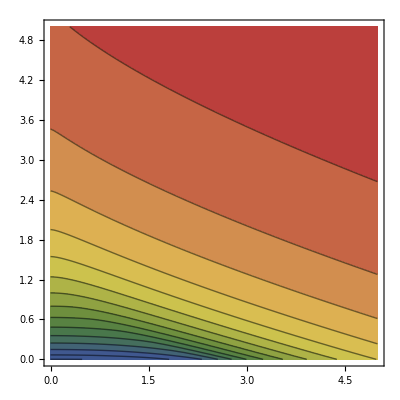
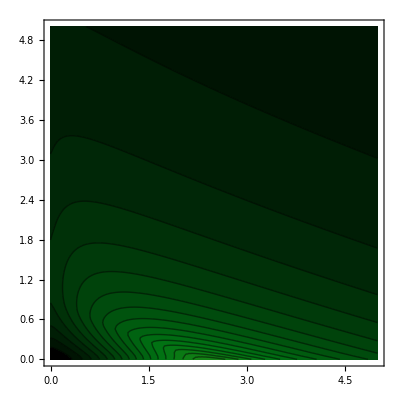
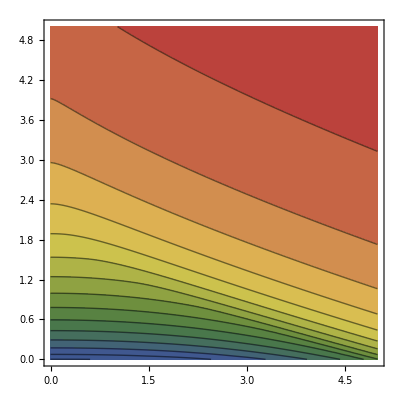
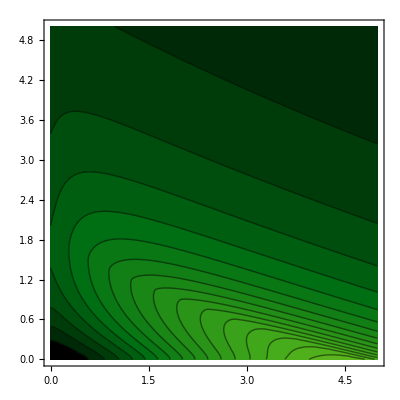
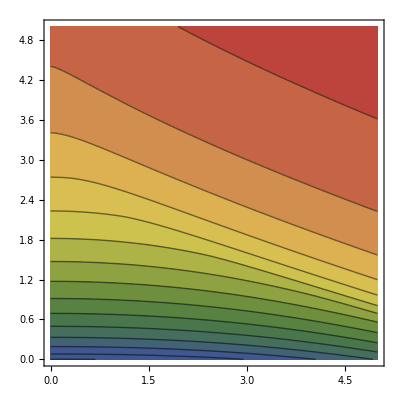
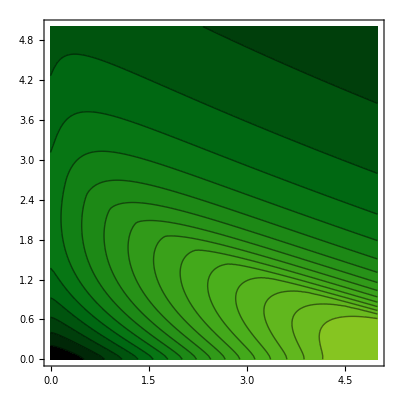
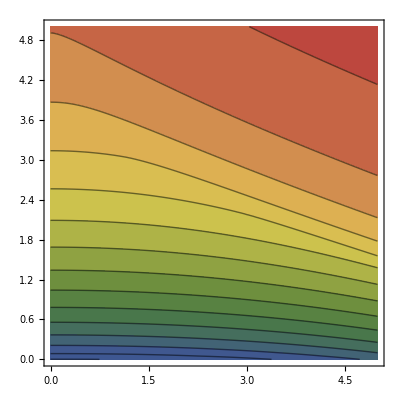
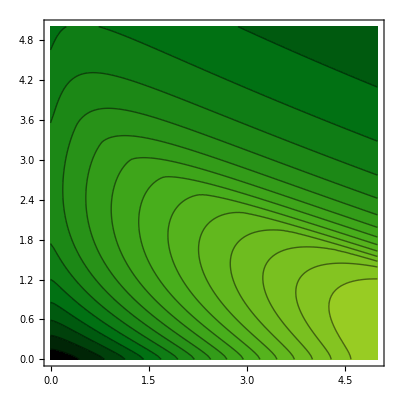
{{-Graphics3D-,-Graphics-,-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-,-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-,-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-,-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-,-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-,-Graphics3D-,-Graphics-}}

```mathematica
plots=Table[genPlotsGeneralCase[a],{a,-0.5,-3,-0.5}]
```

```mathematica
(ExportToIMGFolder[plots[[#[[1]]]][[1]],"l-e-general-3dplot"<>#[[2]]];
ExportToIMGFolder[plots[[#[[1]]]][[2]],"l-e-general-contourplot"<>#[[2]]];
ExportToIMGFolder[plots[[#[[1]]]][[3]],"l-e-general-gain3dplot"<>#[[2]]];
ExportToIMGFolder[plots[[#[[1]]]][[4]],"l-e-general-gaincontourplot"<>#[[2]]];)&/@{
{1,"05"},
{2,"1"},
{3,"15"},
{4,"2"},
{5,"25"},
{6,"3"}
}
```

{Null,Null,Null,Null,Null,Null}

```mathematica
plots2=Table[genPlotsGeneralCase[a,2],{a,-0.5,-3,-0.5}]
```

{{-Graphics3D-,-Graphics-,-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-,-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-,-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-,-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-,-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-,-Graphics3D-,-Graphics-}}

```mathematica
(ExportToIMGFolder[plots2[[#[[1]]]][[1]],"2-l-e-general-3dplot"<>#[[2]]];
ExportToIMGFolder[plots2[[#[[1]]]][[2]],"2-l-e-general-contourplot"<>#[[2]]];
ExportToIMGFolder[plots2[[#[[1]]]][[3]],"2-l-e-general-gain3dplot"<>#[[2]]];
ExportToIMGFolder[plots2[[#[[1]]]][[4]],"2-l-e-general-gaincontourplot"<>#[[2]]];)&/@{
{1,"05"},
{2,"1"},
{3,"15"},
{4,"2"},
{5,"25"},
{6,"3"}
}
```

{Null,Null,Null,Null,Null,Null}